# Amazon Reviews Sentiment Analysis

## Mahsa Moslehi (email: moslehi@usc.edu)

## Aim of the Study

We are given a dataset that contains 400,000 reviews on Amazon and their corresponding labels which specify whether the review is positive or negative. Our main goal is to use the available dataset to design Learning algorithms that classify reviews as positive or negative. Such analysis in Machine Learning (ML) is called Sentiment Analysis.

## Importing Dataset-3 (Amazon Reviews)

```mathematica
raw=OpenRead["reviews.csv"];
```

```mathematica
reviews=Map[StringSplit[#,"|"]&,ReadList[raw,String]];
```

## Extracting Training and Test Sets

In order to perform the analysis, the provided dataset is separated into two sets, training set and test set which contain 80% and 20% of the dataset, respectively. The dataset is divided into two sets such that every 5th sample belongs to test set and the remaining samples belong to training set. Since training learning algorithms using the entire training set is computationally expensive and the goal of this study is mainly discussing the ML steps rather than obtaining the most efficient and accurate classifier, we decided to use a subset of the training set to train the algorithm (8000 samples for training set and 2000 samples for test set). The choice of 8000 samples for training classifiers is achieved by training classifiers (e.g. neural network) with different numbers of samples and observing that above certain numbers of samples, the performance (e.g. accuracy) is not improving significantly, while the running time is increasing easily. This observation is illustrated in the following two plots. Considering this trade-off between the computational time and the classifier’s performance, we decided to select 8000 and 2000 as the size of our train and test subsets, respectively. The train and test subsets are uniformly distributed over the original train and test sets to make sure that the entire dataset is covered.

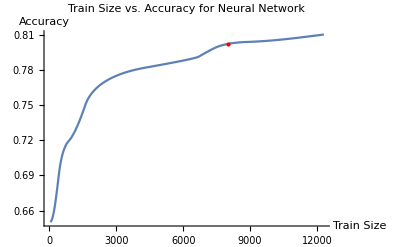

```mathematica
ListLinePlot[{{50,0.65},{150,0.655},{300,0.672},{600,0.709},{1200,0.73},{2500,0.77},{6038,0.788},{6957,0.794},{8000,0.802},{10000,0.805},{12308,0.81}},AxesLabel->{"Train Size","Accuracy"},BaseStyle->{FontSize->12},PlotLabel->"Train Size vs. Accuracy for Neural Network",InterpolationOrder->2,Epilog->{Red,PointSize[Large],Point[{8000,0.802}]}]
```

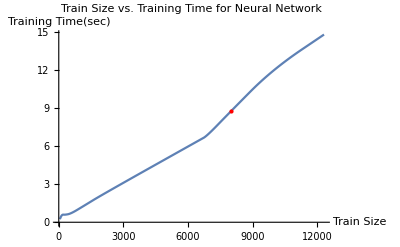

```mathematica
ListLinePlot[{{50,0.2454},{150,0.5572},{300,0.6},{600,0.74},{1200,1.33},{2500,2.63},{6038,6.01},{6957,6.98},{8000,8.77},{10000,12.01},{12308,14.8}},AxesLabel->{"Train Size","Training Time(sec)"},BaseStyle->{FontSize->12},PlotLabel->"Train Size vs. Training Time for Neural Network",InterpolationOrder->2,Epilog->{Red,PointSize[Large],Point[{8000,8.77}]}]
```

In most of the ML experiments, the dataset is separated into 3 groups, training set, validation set and test set. Validation set is usually used to tune the learning algorithm and set the algorithm's parameters (e.g. number of hidden layers in Artificial Neural Network classifier). Alternatively, cross-validation techniques such as k-fold cross-validation can be performed. In k-fold cross-validation, the original sample is randomly partitioned into k equal size sub-samples. Of the k sub-samples, a single sub-sample is retained as the validation data for testing the model, and the remaining k-1 sub-samples are used as training data. The cross-validation process is then repeated k times (the folds), with each of the k sub-samples used exactly once as the validation data. The k results from the folds can then be averaged or combined to produce a single estimation. The advantage of this method is that all observations are used for both training and validation, and each observation is used for validation exactly once. 

Using cross-validation can increase the performance of the classifier, while more computational time is normally required to obtain a high-performance classifier. Therefore, we have decided to skip the cross-validation step mainly because of reducing the running-time and the fact that tuning the learning algorithm parameters and consequently optimizing the algorithm is already implemented in "Classify" function in Mathematica which is the function used in this study.

```mathematica
allTest = Take[reviews, {6,-1,5}];
allTrain = Drop[reviews, {1,-1,5}];
```

```mathematica
sampleFactor=40;
train=Take[allTrain,{1,-1,sampleFactor}];
test=Take[allTest,{1,-1,sampleFactor}];
```

```mathematica
nTrain= Dimensions[train][[1]];
nTest=Dimensions[test][[1]];
```

## Data Preprocessing for Classification

After collecting training and test sets from the original dataset, we need to extract features to input and train the learning model. Since we are dealing with texts in reviews, some text normalizations are required to begin the feature extraction processes such as n-grams. Such text normalization includes changing all strings to lower case and extracting some common words such as, “the”, “I”, “am”, “is”, “are”, etc. 

To perform the feature extraction and classification, I tried various methods described as follows:

1-  Preprocessing Methods employed for Classification using Random Forest, Neural Network and Support vector Machines:

1.1- Find the count of each word used in the reviews from the positive and negative reviews and collect m/2 (where m is the total number of features) number of words from the most frequently-used words in positive reviews. Then, to evaluate the value of the features for each review, a simple approach is to examine whether a review contains that feature (i.e. selected words as features) or not. If it contains the feature, the value will be 1; otherwise, 0.

1.2- Another approach is to modify the first method by assigning the number of occurrence of the features in the reviews as their values. Meaning that instead of assigning 0 or 1 to the value of feature, find the number of occurrence of each feature (i.e. selected words as features) in the review and consider the it as the value of the feature. 

1.3- Furthermore, the above approaches can be both done by considering most frequently -used bi-grams (or in general n-grams) instead of words as features. Meaning that, m/2 most frequently-used bi-grams in positive reviews and m/2 most frequently-used bi-grams in negative reviews can be used as features. Then, the value of features for each review can be evaluated using the description stated in the first or second methods. 

1.4- In this method, after normalizing the reviews (i.e. converting the text to lower case and removing stop words), we first extract all the words in all of the positive and negative reviews and put them into two separate bags. Similarly, we extract all the bi-grams from all of the positive and negative reviews and put them into two separate bags.  In the next step, we compute the frequency of each word and bi-gram with respect to their associated bags. We negate the frequency of the words and bi-grams in the negative bags. Therefore, the frequency for words in negative reviews is negative, but for words in positive reviews is positive. 
Then, we merge the results by adding these frequencies for common words. In the end, we will have weights for each word that its value could be either negative or positive. Similar process is used for bi-grams to obtain the weights for bi-grams. Then, we use these weights to encode all the reviews and prepare them for our training process. Once we receive a review, we convert it to a bag of bi-grams. Then we look up the value of the weights that we computed in the pre-processing step. If, for example, one bi-gram does not exists in our preprocessed weights, we look up the weights associated with each word within the bi-gram and used that as the value of our encoder. Therefore, by this process, each review will be converted to a vector of positive and negative numbers. If a vector has many elements with large positive numbers, it is very likely that the review is a positive review. 

All of the above preprocessing methods have been employed for classification. The fastest one (1.4) is chosen since besides the high efficiency, it results in a reasonable accuracy which keeps the classification highly-performed. 

2-  Preprocessing Method employed for Classification using Markov

2.1- The subset extracted from the original dataset, which contain the reviews in text and their corresponding labels, is used to design a classification using Markov. The reason that we only applied this method on Markov is that, based on Mathematica’s description, Markov can be applied on texts as features. Meaning that, no preprocessing is required for this method and the Classify function with Method Markov can handle the text in the reviews automatically. 

3-  Preprocessing Method employed for Classification using Logistic Regression

3.1- First, each review is converted to a list words (lower case and without stop words). Then, a subset of the train set (1000 reviews) are used to extract features using FeatureExtraction function with technique “TFIDF” in Mathematica. Also, “DimensionReducedVector“ is utilized to increase the efficiency of the training. Then, the original training subset (with 8000 samples) is used to construct the classifier with Classify function using Method LogisticRegression. The reason that other Methods is not used is that classification using feature extraction TFIDF requires a lot computational time even with DimensionReducedVector, and it was only efficient with Logistic Regression method.

### Defining Functions for Text Normalizations for 1.4 and 2.1

```mathematica
removeStopWords[words_]:=DeleteCases[words,Alternatives@@stopwords];
stopwords={"the","i","a","and","to","of","or","at","if","it","this","is","in","was","that","for","from","have","as","be","on","you","with","are","has","had","he","she","his","her"};
```

```mathematica
unigramTokenizer[sentences_]:=removeStopWords@ToLowerCase@StringCases[sentences,(WordCharacter|"'"|"-")..];
bigramTokenizer[words_]:=MapThread[{#1,#2}&]@{words[[;;-2]],words[[2;;]]}
```

### Extracting Uni-gram/Bi-grams for Positive and Negative Reviews for 1.4

```mathematica
posWords=unigramTokenizer@StringJoin[#[[2]]&/@Select[train,#[[1]]=="positive"&]];
negWords=unigramTokenizer@StringJoin[#[[2]]&/@Select[train,#[[1]]=="negative"&]];
```

```mathematica
posBi=bigramTokenizer@unigramTokenizer@StringJoin[#[[2]]&/@Select[train,#[[1]]=="positive"&]];
negBi=bigramTokenizer@unigramTokenizer@StringJoin[#[[2]]&/@Select[train,#[[1]]=="negative"&]];
```

### Defining a Function for Feature Extraction for 1.4

```mathematica
weights=Merge[Total]@{nTrain*N@Counts@posWords/Length[posWords],nTrain*N@-#&/@Counts@negWords/Length[negWords]};
weightsBi=Merge[Total]@{nTrain*N@Counts@posBi/Length[posBi],nTrain*N@-#&/@Counts@negBi/Length[negBi]};
```

```mathematica
encoder[review_]:=Lookup[weightsBi,Key[#],0.1*Total@Lookup[weights,#,0]]&/@bigramTokenizer@unigramTokenizer@review
```

### Defining a Function for Feature Extraction for 3.1

```mathematica
feSetLR=unigramTokenizer@#&/@train[[;;1000,2]];
feLR=FeatureExtraction[feSetLR,{"TFIDF","DimensionReducedVector"}];
```

## Classifications

Next, the encoder function defined above will be used on the training dataset via FeatureExtraction function to obtain the features, which will eventually be used together with their corresponding labels to design the ML classifier. Using the preprocessing technique described in 1.4, three different classification algorithms are used: Random Forest (RF), Artificial Neural Network (ANN), and Support Vector Machine (SVM). The first two algorithms, RF (which is an ensemble variant of Decision Tree) and ANN, are mandatory based on the homework description. The third one, SVM, is chosen since it is widely used in the real-world text classification problems. Moreover, one advantage of using an SVM instead of a Logistic Regression is that our problem might not be linearly separable. In that case, an SVM with a non-linear kernel (e.g. RBF) can be applied to address the classification problem. Note that a Logistic Regression can also be used with a different kernel, but due to practical reasons SVMs are more commonly used when dealing with problems might not be linearly separable. Another reason to use SVMs is if you are in a highly dimensional space. For example, SVMs have been reported to work better for text classification which is our problem. Also, SVMs are usually less susceptible to noise and outlier points as presented in practical ML experiments (References: Coursera ML course taught by Andrew NG). However, one of the downsides of using SVMs is that running time is relatively large, especially when dealing with large training sets. 

Alternatively, classification has been performed using Markov and Logistic Regression algorithms with different preprocessing techniques which are described separately in 2.1 and 3.1 in “Data Preprocessing for Classification” section. The reason that I have included the results of these two algorithms in the report is that they both result in highly-performed and efficient classifiers (e.g. accuracy around 83% and running time less around a few seconds).

In order to train the classifier algorithm, “Classify” function Mathematica has been used. Several parameters in this function can be specified, such as the “Method” employed for the classification and the function utilized for feature extraction. Furthermore, there is an option named “PerformanceGoal” where you can specify whether you want your model to be optimized in terms of “Memory”, ”Quality”, “Speed” or “TrainingSpeed”.

```mathematica
trainingset=#[[2]]->#[[1]]&/@train; (* train set for methods 1.4 and 2.1 *)
```

```mathematica
trainingsetLR=unigramTokenizer@#[[2]]->#[[1]]&/@train; (* train set for method 3.1 *)
```

### Neural Network (1.4)

```mathematica
nn=Classify[trainingset,FeatureExtractor->encoder,Method->"NeuralNetwork"];
```

### Random Forest (1.4)

```mathematica
rf=Classify[trainingset,FeatureExtractor->encoder,Method->"RandomForest"];
```

### Support Vector Machines (1.4)

```mathematica
svm=Classify[trainingset,FeatureExtractor->encoder,Method->{"SupportVectorMachine","KernelType"->"Linear","SoftMarginParameter"->2}];
```

### Markov (2.1)

```mathematica
markov=Classify[trainingset,Method->"Markov"];
```

### Logistic Regression (3.1)

```mathematica
lr=Classify[trainingsetLR,FeatureExtractor->feLR,Method->"LogisticRegression"];
```

## Results

In this section, the trained classifiers, obtained from the previous section, are used to achieve the accuracy, precision, recall, confusion matrix plot, ROC curves and the area under ROC curves of the classifiers using the test set. In Mathematica, “ClassifierMeasurements” function can be used to evaluate all the required performance metrics and visualizations.

```mathematica
testset=#[[2]]->#[[1]]&/@test; (* test set for methods 1.4 and 2.1 *)
```

```mathematica
testsetLR=unigramTokenizer@#[[2]]->#[[1]]&/@test;  (* test set for method 3.1 *)
```

### Neural Network (1.4)

```mathematica
cmNN=ClassifierMeasurements[nn,testset];
```

```mathematica
accNN=cmNN["Accuracy"]
```

0.804

```mathematica
precNN=cmNN["Precision"]
```

<|negative→0.785714,positive→0.825991|>

```mathematica
recNN=cmNN["Recall"]
```

<|negative→0.844488,positive→0.762195|>

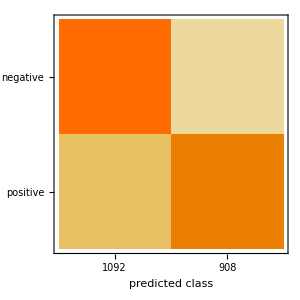

```mathematica
confMtxNN=cmNN["ConfusionMatrixPlot"]
```

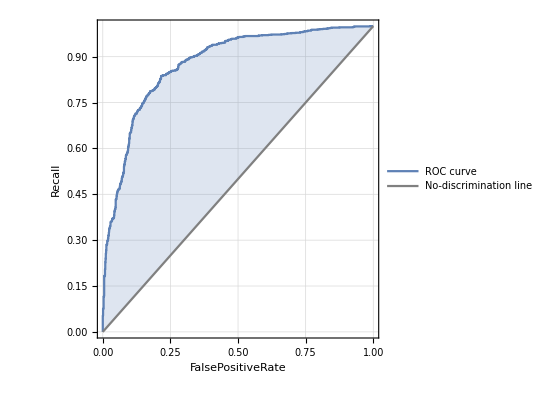
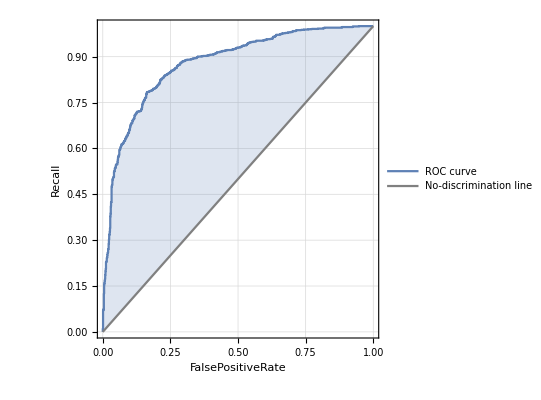
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
rocNN=cmNN["ROCCurve"]
```

```mathematica
rocAreaNN=cmNN["AreaUnderROCCurve"]
```

<|negative→0.878252,positive→0.878252|>

### Random Forest (1.4)

```mathematica
cmRF=ClassifierMeasurements[rf,testset];
```

```mathematica
accRF=cmRF["Accuracy"]
```

0.797

```mathematica
precRF=cmRF["Precision"]
```

<|negative→0.820378,positive→0.775763|>

```mathematica
recRF=cmRF["Recall"]
```

<|negative→0.768701,positive→0.82622|>

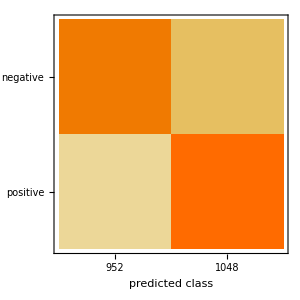

```mathematica
confMtxRF=cmRF["ConfusionMatrixPlot"]
```

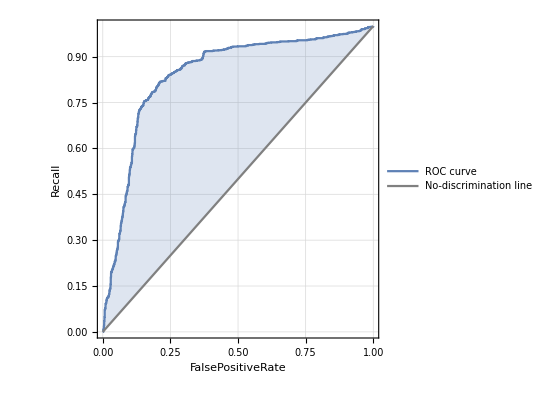
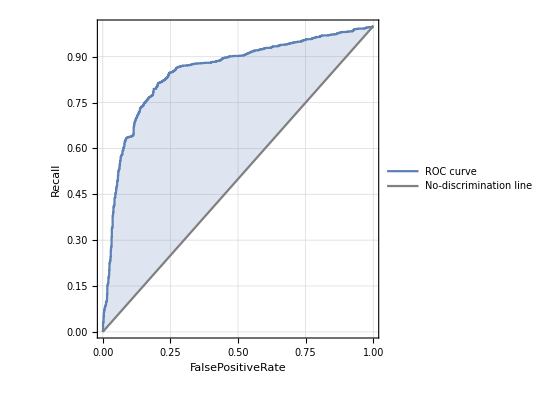
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
rocRF=cmRF["ROCCurve"]
```

```mathematica
rocAreaRF=cmRF["AreaUnderROCCurve"]
```

<|negative→0.843152,positive→0.852211|>

### Support Vector Machines (1.4)

```mathematica
cmSVM=ClassifierMeasurements[svm,testset];
```

```mathematica
accSVM=cmSVM["Accuracy"]
```

0.8035

```mathematica
precSVM=cmSVM["Precision"]
```

<|negative→0.798086,positive→0.809424|>

```mathematica
recSVM=cmSVM["Recall"]
```

<|negative→0.820866,positive→0.785569|>

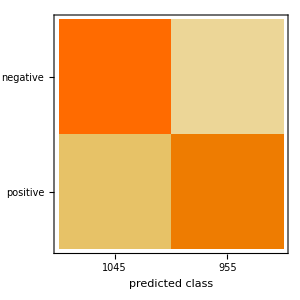

```mathematica
confMtxSVM=cmSVM["ConfusionMatrixPlot"]
```

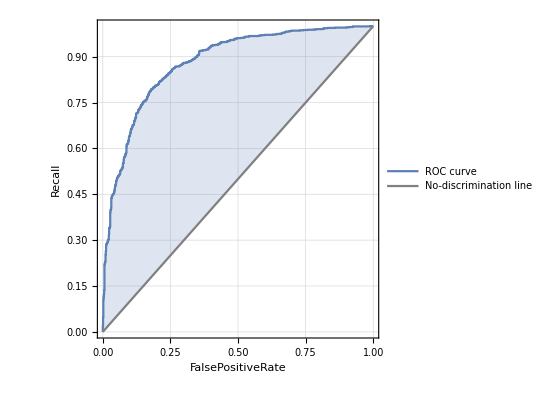
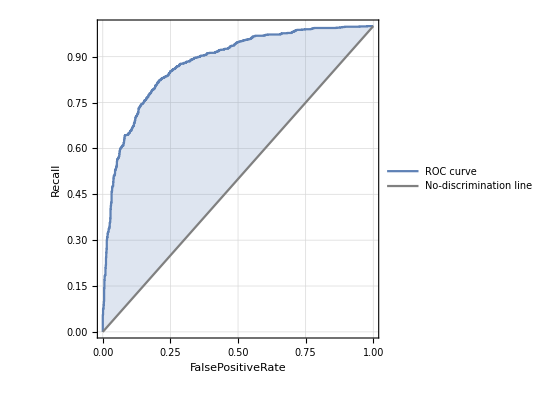
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
rocSVM=cmSVM["ROCCurve"]
```

```mathematica
rocAreaSVM=cmSVM["AreaUnderROCCurve"]
```

<|negative→0.881184,positive→0.881235|>

### Markov (2.1)

```mathematica
cmMarkov=ClassifierMeasurements[markov,testset];
```

```mathematica
accMarkov=cmMarkov["Accuracy"]
```

0.837

```mathematica
precMarkov=cmMarkov["Precision"]
```

<|negative→0.81768,positive→0.859956|>

```mathematica
recMarkov=cmMarkov["Recall"]
```

<|negative→0.874016,positive→0.79878|>

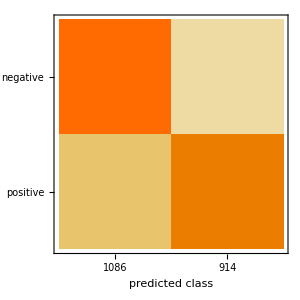

```mathematica
confMtxMarkov=cmMarkov["ConfusionMatrixPlot"]
```

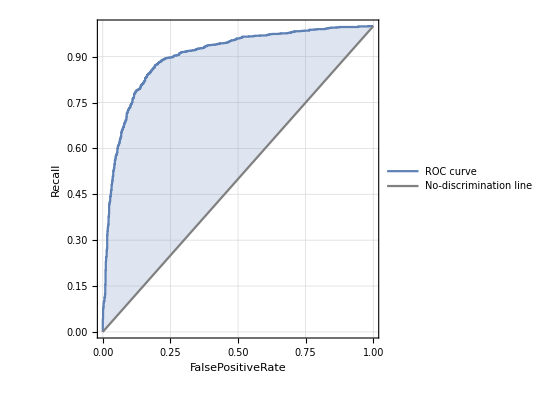
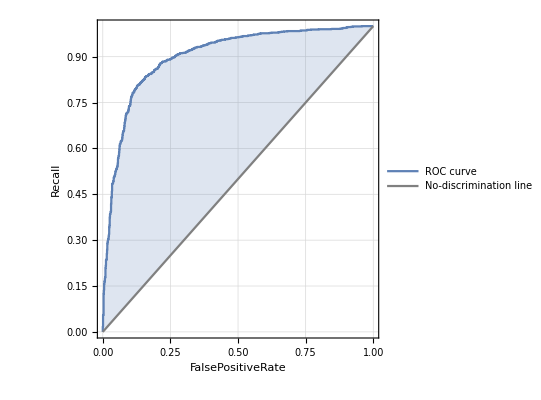
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
rocMarkov=cmMarkov["ROCCurve"]
```

```mathematica
rocAreaMarkov=cmMarkov["AreaUnderROCCurve"]
```

<|negative→0.901912,positive→0.901912|>

### Logistic Regression (3.1)

```mathematica
cmLR=ClassifierMeasurements[lr,testsetLR];
```

```mathematica
accLR=cmLR["Accuracy"]
```

0.835

```mathematica
precLR=cmLR["Precision"]
```

<|negative→0.829175,positive→0.841336|>

```mathematica
recLR=cmLR["Recall"]
```

<|negative→0.850394,positive→0.819106|>

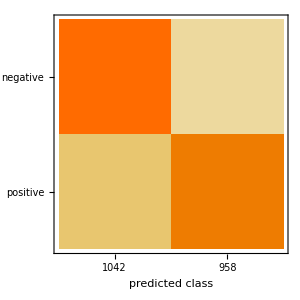

```mathematica
confMtxLR=cmLR["ConfusionMatrixPlot"]
```

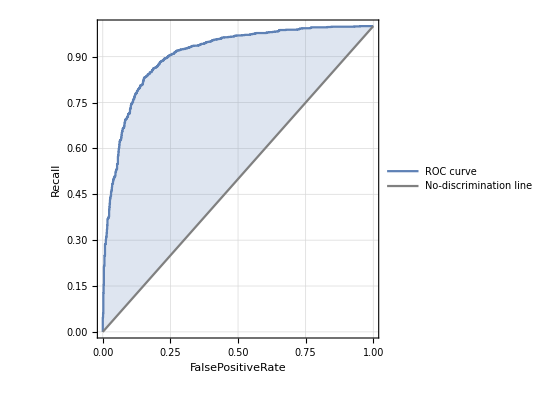
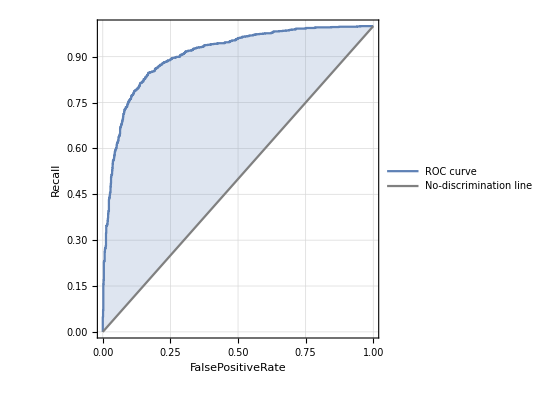
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
rocLR=cmLR["ROCCurve"]
```

```mathematica
rocAreaLR=cmLR["AreaUnderROCCurve"]
```

<|negative→0.907923,positive→0.907923|>

## Comparison of Results Obtained from Classification Algorithms

### Accuracy

```mathematica
Accuracies=TableForm[{accNN,accRF,accSVM, accMarkov, accLR},
TableHeadings->{{"Neural Networks","Random Forest","Support Vector Machines", "Markov", "Logostic Regression"},{"Accuracy"}}]
```

Neural Networks | 0.804
Random Forest | 0.797
Support Vector Machines | 0.8035
Markov | 0.837
Logostic Regression | 0.835

### Precision

```mathematica
precisions=TableForm[Reverse@Values@#&/@{precNN,precRF,precSVM, precMarkov,precLR},
TableHeadings->{{"Neural Networks","Random Forest","Support Vector Machines", "Markov", "Logostic Regression"},{"Precision(Positive)","Precision(Negative)"}}]
```

| Precision(Positive) | Precision(Negative)
Neural Networks | 0.825991 | 0.785714
Random Forest | 0.775763 | 0.820378
Support Vector Machines | 0.809424 | 0.798086
Markov | 0.859956 | 0.81768
Logostic Regression | 0.841336 | 0.829175

### Recall

```mathematica
Recalls=TableForm[Reverse@Values@#&/@{recNN,recRF,recSVM, recMarkov, recLR},
TableHeadings->{{"Neural Networks","Random Forest","Support Vector Machines", "Markov", "Logostic Regression"},{"Recall(Positive)","Recall(Negative)"}}]
```

| Recall(Positive) | Recall(Negative)
Neural Networks | 0.762195 | 0.844488
Random Forest | 0.82622 | 0.768701
Support Vector Machines | 0.785569 | 0.820866
Markov | 0.79878 | 0.874016
Logostic Regression | 0.819106 | 0.850394

### Area Under ROC Curve

```mathematica
rocAreas=TableForm[Reverse@Values@#&/@{rocAreaNN,rocAreaRF,rocAreaSVM, rocAreaMarkov, rocAreaLR},
TableHeadings->{{"Neural Networks","Random Forest","Support Vector Machines", "Markov", "Logostic Regression"},{"Area Under ROC(Positive)","Area under ROC(Negative)"}}]
```

| Area Under ROC(Positive) | Area under ROC(Negative)
Neural Networks | 0.878252 | 0.878252
Random Forest | 0.852211 | 0.843152
Support Vector Machines | 0.881235 | 0.881184
Markov | 0.901912 | 0.901912
Logostic Regression | 0.907923 | 0.907923

## Conclusions and Recommendations

Here, we only presented some approaches to address the above text classification problem. There are many other methods out there to tackle such problems. The purpose of this study was to present a general ML pipeline, try several preprocessing techniques and classification algorithms, and eventually discuss the results associated with them. From the above ML experiment, it can be observed that all three classification algorithms with preprocessing technique stated in (1.4) result in classifiers with similar accuracy (around %80). Precisions and Recalls obtained from all algorithms are also similar. However, the difference between the results in the metric “Area under ROC Curves” is more noticeable. It can be observed that Random Forest produced lower values for that area under ROC curve metric, which indicates lower performance comparing to the other two classifiers. However, Support Vector Machine algorithm has a better performance with respect to area under ROC comparing to Neural Networks and Random Forest. The other two classifiers, Markov (2.1) and Logistic Regression (3.1), we have achieved higher performance (e.g. accuracy) and yet relatively efficient classifiers. However, the preprocessing techniques used for these two are not employed for Random Forest, Neural Network and Support Vector Machine methods since the running time would be very large (i.e. may not be tractable on regular computers). It should be noted that the above conclusions are limited to the configuration (e.g. number of samples and the technique employed for preprocessing and feature extraction) considered in this study.   

There are various ways to increase the efficiency and performance of the classification model. For example, increasing the number of training set can enhance the accuracy of the classifier, especially when the features are selected such that they can predict the labels accurately. Increasing the number of features can also help to boost the performance of the classifier. However, it should be noted that if the number of features are too large, overfitting problem might occur. Another way to improve the performance is to implement cross validation in the analysis which will create an ensemble of the algorithms, as described in section “Extracting Training and Test Sets”.  Moreover, increasing the number of trees in Random Forest can help us to achieve more reliable predictors. In general, using Ensemble Machine Learning, where multiple learners are trained to solve the same problem, can increase the performance of the classification since it constructs a set of hypotheses and combine them to use.